```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=√(m^2+p^2);Nx=10;
```

```mathematica
α=1;m =5/2;λ=π/2;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_]:=ω[p]ϕ[n][p]-λ Integrate[(ϕ[n][k]-ϕ[n][p])/(p-k)^2,{k,-∞,∞},PrincipalValue->True,GenerateConditions->False]
```

```mathematica
Table[Integrate[ϕ[2i][p]H[2n],{p,-∞,∞},GenerateConditions->False],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
```

{4699.81,{{(1/2+ⅈ/2) π^(3/2)+HypergeometricU[-1/2,0,25/4],((-4-4 ⅈ) π^2+25 ⅇ^(25/8) (-BesselK[0,25/8]+BesselK[1,25/8]))/(8 √(2 π)),((24+24 ⅈ) π^2+25 ⅇ^(25/8) (31 BesselK[0,25/8]-27 BesselK[1,25/8]))/(32 √(6 π)),-1/384 √(5/π) ((48+48 ⅈ) π^2+5 ⅇ^(25/8) (1135 BesselK[0,25/8]-987 BesselK[1,25/8])),1/512 √(5/(14 π)) ((224+224 ⅈ) π^2+25 ⅇ^(25/8) (3281 BesselK[0,25/8]-2853 BesselK[1,25/8])),((-12096-12096 ⅈ) π^2+25 ⅇ^(25/8) (-489899 BesselK[0,25/8]+425991 BesselK[1,25/8]))/(18432 √(7 π)),((266112+266112 ⅈ) π^2+25 ⅇ^(25/8) (27403403 BesselK[0,25/8]-23828583 BesselK[1,25/8]))/(73728 √(231 π)),-((2306304+2306304 ⅈ) π^2+25 ⅇ^(25/8) (565611601 BesselK[0,25/8]-491826597 BesselK[1,25/8]))/(344064 √(858 π)),(√(55/(26 π)) ((3773952+3773952 ⅈ) π^2+5 ⅇ^(25/8) (10452866665 BesselK[0,25/8]-9089272221 BesselK[1,25/8])))/24772608,-(√(5/(2431 π)) ((1411458048+1411458048 ⅈ) π^2+25 ⅇ^(25/8) (1689979837087 BesselK[0,25/8]-1469519057931 BesselK[1,25/8])))/297271296,((1986496512+1986496512 ⅈ) π^2+25 ⅇ^(25/8) (4952292298253 BesselK[0,25/8]-4306257241617 BesselK[1,25/8]))/(44040192 √(46189 π))},{((-4+4 ⅈ) π^2+25 ⅇ^(25/8) (-BesselK[0,25/8]+BesselK[1,25/8]))/(8 √(2 π)),((8-8 ⅈ) π^2+75 ⅇ^(25/8) (9 BesselK[0,25/8]-5 BesselK[1,25/8]))/(32 √π),((-48+48 ⅈ) π^2+75 ⅇ^(25/8) (-229 BesselK[0,25/8]+201 BesselK[1,25/8]))/(128 √(3 π)),1/256 √(5/(2 π)) ((32-32 ⅈ) π^2+15 ⅇ^(25/8) (2855 BesselK[0,25/8]-2483 BesselK[1,25/8])),(√(35/π) ((-64+64 ⅈ) π^2+5 ⅇ^(25/8) (-53755 BesselK[0,25/8]+46743 BesselK[1,25/8])))/2048,((8064-8064 ⅈ) π^2+25 ⅇ^(25/8) (3783641 BesselK[0,25/8]-3290061 BesselK[1,25/8]))/(12288 √(14 π)),((-59136+59136 ⅈ) π^2+25 ⅇ^(25/8) (-71126459 BesselK[0,25/8]+61847895 BesselK[1,25/8]))/(16384 √(462 π)),((4612608-4612608 ⅈ) π^2+25 ⅇ^(25/8) (13302820577 BesselK[0,25/8]-11567444853 BesselK[1,25/8]))/(1376256 √(429 π)),(√(5/(143 π)) ((-27675648+27675648 ⅈ) π^2+5 ⅇ^(25/8) (-906680821385 BesselK[0,25/8]+788402748477 BesselK[1,25/8])))/33030144,(√(65/(374 π)) ((24127488-24127488 ⅈ) π^2+5 ⅇ^(25/8) (1717129193935 BesselK[0,25/8]-1493126734587 BesselK[1,25/8])))/66060288,((-35756937216+35756937216 ⅈ) π^2+25 ⅇ^(25/8) (-1064421711988429 BesselK[0,25/8]+925566067068369 BesselK[1,25/8]))/(792723456 √(92378 π))},{((-8-8 ⅈ) π^2+25 ⅇ^(25/8) (31 BesselK[0,25/8]-27 BesselK[1,25/8]))/(32 √(6 π)),((16+16 ⅈ) π^2+75 ⅇ^(25/8) (-229 BesselK[0,25/8]+201 BesselK[1,25/8]))/(128 √(3 π)),((-96-96 ⅈ) π^2+25 ⅇ^(25/8) (21247 BesselK[0,25/8]-18027 BesselK[1,25/8]))/(1536 √π),(√(5/(6 π)) ((192+192 ⅈ) π^2+25 ⅇ^(25/8) (-158219 BesselK[0,25/8]+137703 BesselK[1,25/8])))/3072,-(√(5/(21 π)) ((896+896 ⅈ) π^2+5 ⅇ^(25/8) (-11674685 BesselK[0,25/8]+10151937 BesselK[1,25/8])))/8192,((48384+48384 ⅈ) π^2+25 ⅇ^(25/8) (-354266963 BesselK[0,25/8]+308052687 BesselK[1,25/8]))/(147456 √(42 π)),-(√(7/(22 π)) ((152064+152064 ⅈ) π^2+25 ⅇ^(25/8) (-2868142373 BesselK[0,25/8]+2493988617 BesselK[1,25/8])))/1769472,((3075072+3075072 ⅈ) π^2+25 ⅇ^(25/8) (-139653575779 BesselK[0,25/8]+121435528479 BesselK[1,25/8]))/(5505024 √(143 π)),-(√(5/(429 π)) ((166053888+166053888 ⅈ) π^2+25 ⅇ^(25/8) (-17194801738591 BesselK[0,25/8]+14951710284747 BesselK[1,25/8])))/396361728,(√(5/(14586 π)) ((5645832192+5645832192 ⅈ) π^2+5 ⅇ^(25/8) (-6370195058283395 BesselK[0,25/8]+5539192147528383 BesselK[1,25/8])))/2378170368,-(√(13/(21318 π)) ((5501067264+5501067264 ⅈ) π^2+25 ⅇ^(25/8) (-2603483413986673 BesselK[0,25/8]+2263854520325445 BesselK[1,25/8])))/3170893824},{((-48+48 ⅈ) π^2+25 ⅇ^(25/8) (-1135 BesselK[0,25/8]+987 BesselK[1,25/8]))/(384 √(5 π)),((32-32 ⅈ) π^2+75 ⅇ^(25/8) (2855 BesselK[0,25/8]-2483 BesselK[1,25/8]))/(256 √(10 π)),((-9+9 ⅈ) π^2-125/64 ⅇ^(25/8) (158219 BesselK[0,25/8]-137703 BesselK[1,25/8]))/(48 √(30 π)),((180-180 ⅈ) π^2+625/32 ⅇ^(25/8) (1200463 BesselK[0,25/8]-1041531 BesselK[1,25/8]))/(5760 √π),((-5376+5376 ⅈ) π^2+125 ⅇ^(25/8) (-17786269 BesselK[0,25/8]+15467745 BesselK[1,25/8]))/(49152 √(14 π)),((290304-290304 ⅈ) π^2+25 ⅇ^(25/8) (13551477155 BesselK[0,25/8]-11783705439 BesselK[1,25/8]))/(1769472 √(35 π)),(√(7/(165 π)) ((-912384+912384 ⅈ) π^2+25 ⅇ^(25/8) (-110106373805 BesselK[0,25/8]+95742833457 BesselK[1,25/8])))/7077888,((810810-810810 ⅈ) π^2+(1875 ⅇ^(25/8) (3226611252149 BesselK[0,25/8]-2805694340313 BesselK[1,25/8]))/1024)/(483840 √(4290 π)),((-996323328+996323328 ⅈ) π^2+125 ⅇ^(25/8) (-132779499898907 BesselK[0,25/8]+115458185978679 BesselK[1,25/8]))/(2378170368 √(286 π)),((206756550-206756550 ⅈ) π^2+(3125 ⅇ^(25/8) (9861485262022763 BesselK[0,25/8]-8575037536123335 BesselK[1,25/8]))/4096)/(174182400 √(2431 π)),((-143027748864+143027748864 ⅈ) π^2+25 ⅇ^(25/8) (-437545730217211255 BesselK[0,25/8]+380467136418893763 BesselK[1,25/8]))/(12683575296 √(230945 π))},{-1/512 √(5/(14 π)) ((32+32 ⅈ) π^2+25 ⅇ^(25/8) (-3281 BesselK[0,25/8]+2853 BesselK[1,25/8])),(√(5/(7 π)) ((64+64 ⅈ) π^2+35 ⅇ^(25/8) (-53755 BesselK[0,25/8]+46743 BesselK[1,25/8])))/2048,-(√(5/(21 π)) ((384+384 ⅈ) π^2+5 ⅇ^(25/8) (-11674685 BesselK[0,25/8]+10151937 BesselK[1,25/8])))/8192,(5 ((768+768 ⅈ) π^2+25 ⅇ^(25/8) (-17786269 BesselK[0,25/8]+15467745 BesselK[1,25/8])))/(49152 √(14 π)),-(5 ((1536+1536 ⅈ) π^2+25 ⅇ^(25/8) (-113533963 BesselK[0,25/8]+98696679 BesselK[1,25/8])))/(393216 √π),(√(5/(2 π)) ((193536+193536 ⅈ) π^2+25 ⅇ^(25/8) (-40496986613 BesselK[0,25/8]+35214669849 BesselK[1,25/8])))/16515072,-(√(55/(6 π)) ((387072+387072 ⅈ) π^2+5 ⅇ^(25/8) (-1049916312955 BesselK[0,25/8]+912953488407 BesselK[1,25/8])))/66060288,(√(5/(3003 π)) ((110702592+110702592 ⅈ) π^2+5 ⅇ^(25/8) (-726996771836705 BesselK[0,25/8]+632158824885429 BesselK[1,25/8])))/264241152,-(5 ((94887936+94887936 ⅈ) π^2+175 ⅇ^(25/8) (-40790191194409 BesselK[0,25/8]+35469040749405 BesselK[1,25/8])))/(905969664 √(1001 π)),(5 √(13/(2618 π)) ((1737179136+1737179136 ⅈ) π^2+25 ⅇ^(25/8) (-11440415215651013 BesselK[0,25/8]+9947993362816809 BesselK[1,25/8])))/38050725888,-1/152202903552 √(5/(646646 π)) ((858166493184+858166493184 ⅈ) π^2+25 ⅇ^(25/8) (-11898061970899652897 BesselK[0,25/8]+10345939303245939381 BesselK[1,25/8]))},{((-1344+1344 ⅈ) π^2+25 ⅇ^(25/8) (-489899 BesselK[0,25/8]+425991 BesselK[1,25/8]))/(18432 √(7 π)),((896-896 ⅈ) π^2+25 ⅇ^(25/8) (3783641 BesselK[0,25/8]-3290061 BesselK[1,25/8]))/(12288 √(14 π)),((-16128+16128 ⅈ) π^2+25 ⅇ^(25/8) (-354266963 BesselK[0,25/8]+308052687 BesselK[1,25/8]))/(147456 √(42 π)),(√(5/(7 π)) ((32256-32256 ⅈ) π^2+5 ⅇ^(25/8) (13551477155 BesselK[0,25/8]-11783705439 BesselK[1,25/8])))/1769472,(√(5/(2 π)) ((-150528+150528 ⅈ) π^2+25 ⅇ^(25/8) (-40496986613 BesselK[0,25/8]+35214669849 BesselK[1,25/8])))/16515072,((8128512-8128512 ⅈ) π^2+25 ⅇ^(25/8) (6208730570527 BesselK[0,25/8]-5398577836683 BesselK[1,25/8]))/(594542592 √π),((-178827264+178827264 ⅈ) π^2+25 ⅇ^(25/8) (-354944768423719 BesselK[0,25/8]+308642491024179 BesselK[1,25/8]))/(2378170368 √(33 π)),((516612096-516612096 ⅈ) π^2+25 ⅇ^(25/8) (2487599128053791 BesselK[0,25/8]-2163087799652235 BesselK[1,25/8]))/(528482304 √(6006 π)),(√(5/(2002 π)) ((-27897053184+27897053184 ⅈ) π^2+5 ⅇ^(25/8) (-1541532770850614095 BesselK[0,25/8]+1340437182161158779 BesselK[1,25/8])))/114152177664,1/1369826131968 √(5/(17017 π)) ((948499808256-948499808256 ⅈ) π^2+25 ⅇ^(25/8) (22977462998817902051 BesselK[0,25/8]-19980013419610911903 BesselK[1,25/8])),1/786432 √(323323/π) ((-16+16 ⅈ) π^2+3375 ⅇ^(25/8) (4883 BesselK[1,25/8]-2535 BesselK[2,25/8])+288 √π (10005 HypergeometricU[-1/2,-15,25/4]-81075 HypergeometricU[-1/2,-14,25/4]+303025 HypergeometricU[-1/2,-13,25/4]-694255 HypergeometricU[-1/2,-12,25/4]+1092225 HypergeometricU[-1/2,-11,25/4]-1251607 HypergeometricU[-1/2,-10,25/4]+1080445 HypergeometricU[-1/2,-9,25/4]-716115 HypergeometricU[-1/2,-8,25/4]+367695 HypergeometricU[-1/2,-7,25/4]-146345 HypergeometricU[-1/2,-6,25/4]+44803 HypergeometricU[-1/2,-5,25/4]-10365 HypergeometricU[-1/2,-4,25/4]-205 HypergeometricU[-1/2,-2,25/4]-HypergeometricU[-1/2,0,25/4]))},{-((24192+24192 ⅈ) π^2+25 ⅇ^(25/8) (-27403403 BesselK[0,25/8]+23828583 BesselK[1,25/8]))/(73728 √(231 π)),((5376+5376 ⅈ) π^2+25 ⅇ^(25/8) (-71126459 BesselK[0,25/8]+61847895 BesselK[1,25/8]))/(16384 √(462 π)),-(√(7/(22 π)) ((41472+41472 ⅈ) π^2+25 ⅇ^(25/8) (-2868142373 BesselK[0,25/8]+2493988617 BesselK[1,25/8])))/1769472,(√(35/(33 π)) ((82944+82944 ⅈ) π^2+5 ⅇ^(25/8) (-110106373805 BesselK[0,25/8]+95742833457 BesselK[1,25/8])))/7077888,-(√(5/(66 π)) ((2709504+2709504 ⅈ) π^2+55 ⅇ^(25/8) (-1049916312955 BesselK[0,25/8]+912953488407 BesselK[1,25/8])))/66060288,((146313216+146313216 ⅈ) π^2+25 ⅇ^(25/8) (-354944768423719 BesselK[0,25/8]+308642491024179 BesselK[1,25/8]))/(2378170368 √(33 π)),-((3218890752+3218890752 ⅈ) π^2+25 ⅇ^(25/8) (-20332442586751543 BesselK[0,25/8]+17679921877990275 BesselK[1,25/8]))/(313918488576 √π),((27897053184+27897053184 ⅈ) π^2+25 ⅇ^(25/8) (-428228995035535781 BesselK[0,25/8]+372365988767195529 BesselK[1,25/8]))/(209278992384 √(182 π)),-(√(5/(546 π)) ((502146957312+502146957312 ⅈ) π^2+5 ⅇ^(25/8) (-88590300370018904815 BesselK[0,25/8]+77033545132889496219 BesselK[1,25/8])))/5022695817216,1/8610335686656 √(5/(4641 π)) ((2438999506944+2438999506944 ⅈ) π^2+5 ⅇ^(25/8) (-944486239681311137905 BesselK[0,25/8]+821276385749629645893 BesselK[1,25/8])),-1/3826815860736 √(19/(4641 π)) ((541999890432+541999890432 ⅈ) π^2+25 ⅇ^(25/8) (-88607022063098137063 BesselK[0,25/8]+77048083506732518643 BesselK[1,25/8]))},{((-177408+177408 ⅈ) π^2+25 ⅇ^(25/8) (-565611601 BesselK[0,25/8]+491826597 BesselK[1,25/8]))/(344064 √(858 π)),((354816-354816 ⅈ) π^2+25 ⅇ^(25/8) (13302820577 BesselK[0,25/8]-11567444853 BesselK[1,25/8]))/(1376256 √(429 π)),((-709632+709632 ⅈ) π^2+25 ⅇ^(25/8) (-139653575779 BesselK[0,25/8]+121435528479 BesselK[1,25/8]))/(5505024 √(143 π)),(√(5/(858 π)) ((4257792-4257792 ⅈ) π^2+25 ⅇ^(25/8) (3226611252149 BesselK[0,25/8]-2805694340313 BesselK[1,25/8])))/33030144,(√(5/(3003 π)) ((-59609088+59609088 ⅈ) π^2+5 ⅇ^(25/8) (-726996771836705 BesselK[0,25/8]+632158824885429 BesselK[1,25/8])))/264241152,((357654528-357654528 ⅈ) π^2+25 ⅇ^(25/8) (2487599128053791 BesselK[0,25/8]-2163087799652235 BesselK[1,25/8]))/(528482304 √(6006 π)),((-23605198848+23605198848 ⅈ) π^2+25 ⅇ^(25/8) (-428228995035535781 BesselK[0,25/8]+372365988767195529 BesselK[1,25/8]))/(209278992384 √(182 π)),((47210397696-47210397696 ⅈ) π^2+25 ⅇ^(25/8) (2084455170148962937 BesselK[0,25/8]-1812532084761700077 BesselK[1,25/8]))/(5859811786752 √π),1/203140141940736 √(5/(3 π)) ((-1227470340096+1227470340096 ⅈ) π^2+25 ⅇ^(25/8) (-124740646100935428787 BesselK[0,25/8]+108468026524213485999 BesselK[1,25/8])),1/3656522554933248 √(5/(102 π)) ((125201974689792-125201974689792 ⅈ) π^2+5 ⅇ^(25/8) (139804454705735319077645 BesselK[0,25/8]-121566723598913426505489 BesselK[1,25/8])),1/131072 √(323/(6 π)) ((-132+132 ⅈ) π^2+3575 ⅇ^(25/8) (86977 BesselK[1,25/8]-45175 BesselK[2,25/8])+24 √π (10235115 HypergeometricU[-1/2,-17,25/4]-87153555 HypergeometricU[-1/2,-16,25/4]+348454140 HypergeometricU[-1/2,-15,25/4]-869296500 HypergeometricU[-1/2,-14,25/4]+1516169200 HypergeometricU[-1/2,-13,25/4]-1962547496 HypergeometricU[-1/2,-12,25/4]+1952682732 HypergeometricU[-1/2,-11,25/4]-1525674436 HypergeometricU[-1/2,-10,25/4]+947799710 HypergeometricU[-1/2,-9,25/4]-470883270 HypergeometricU[-1/2,-8,25/4]+187105204 HypergeometricU[-1/2,-7,25/4]-59127068 HypergeometricU[-1/2,-6,25/4]+14678664 HypergeometricU[-1/2,-5,25/4]-2802800 HypergeometricU[-1/2,-4,25/4]-39468 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4]))},{-(√(11/(130 π)) ((1257984+1257984 ⅈ) π^2+25 ⅇ^(25/8) (-10452866665 BesselK[0,25/8]+9089272221 BesselK[1,25/8])))/24772608,((9225216+9225216 ⅈ) π^2+25 ⅇ^(25/8) (-906680821385 BesselK[0,25/8]+788402748477 BesselK[1,25/8]))/(33030144 √(715 π)),((-810810-810810 ⅈ) π^2+(625 ⅇ^(25/8) (17194801738591 BesselK[0,25/8]-14951710284747 BesselK[1,25/8]))/1024)/(1935360 √(2145 π)),((332107776+332107776 ⅈ) π^2+125 ⅇ^(25/8) (-132779499898907 BesselK[0,25/8]+115458185978679 BesselK[1,25/8]))/(2378170368 √(286 π)),-(√(7/(143 π)) ((31629312+31629312 ⅈ) π^2+125 ⅇ^(25/8) (-40790191194409 BesselK[0,25/8]+35469040749405 BesselK[1,25/8])))/905969664,((83691159552+83691159552 ⅈ) π^2+25 ⅇ^(25/8) (-1541532770850614095 BesselK[0,25/8]+1340437182161158779 BesselK[1,25/8]))/(114152177664 √(10010 π)),((-89902612800-89902612800 ⅈ) π^2+625/512 ⅇ^(25/8) (88590300370018904815 BesselK[0,25/8]-77033545132889496219 BesselK[1,25/8]))/(245248819200 √(2730 π)),((5319038140416+5319038140416 ⅈ) π^2+125 ⅇ^(25/8) (-124740646100935428787 BesselK[0,25/8]+108468026524213485999 BesselK[1,25/8]))/(203140141940736 √(15 π)),-1/(43878270659198976 √π)((287228059582464+287228059582464 ⅈ) π^2+125 ⅇ^(25/8) (-15522199776874904501023 BesselK[0,25/8]+13497298465790316887691 BesselK[1,25/8])),1/(23933602177744896 √(34 π))((887795820527616+887795820527616 ⅈ) π^2+125 ⅇ^(25/8) (-105545224879914794699237 BesselK[0,25/8]+91776670977996594353865 BesselK[1,25/8])),-1/(351026165273591808 √(3230 π))((123699550993514496+123699550993514496 ⅈ) π^2+25 ⅇ^(25/8) (-155523569237415355658880785 BesselK[0,25/8]+135235252056103249765203813 BesselK[1,25/8]))},{(√(5/(2431 π)) ((-83026944+83026944 ⅈ) π^2+25 ⅇ^(25/8) (-1689979837087 BesselK[0,25/8]+1469519057931 BesselK[1,25/8])))/297271296,(√(65/(374 π)) ((1419264-1419264 ⅈ) π^2+5 ⅇ^(25/8) (1717129193935 BesselK[0,25/8]-1493126734587 BesselK[1,25/8])))/66060288,(√(5/(14586 π)) ((-996323328+996323328 ⅈ) π^2+5 ⅇ^(25/8) (-6370195058283395 BesselK[0,25/8]+5539192147528383 BesselK[1,25/8])))/2378170368,(5 ((1992646656-1992646656 ⅈ) π^2+25 ⅇ^(25/8) (9861485262022763 BesselK[0,25/8]-8575037536123335 BesselK[1,25/8])))/(28538044416 √(2431 π)),(5 √(13/(2618 π)) ((-715309056+715309056 ⅈ) π^2+25 ⅇ^(25/8) (-11440415215651013 BesselK[0,25/8]+9947993362816809 BesselK[1,25/8])))/38050725888,1/1369826131968 √(5/(17017 π)) ((502146957312-502146957312 ⅈ) π^2+25 ⅇ^(25/8) (22977462998817902051 BesselK[0,25/8]-19980013419610911903 BesselK[1,25/8])),1/8610335686656 √(5/(4641 π)) ((-1578176151552+1578176151552 ⅈ) π^2+5 ⅇ^(25/8) (-944486239681311137905 BesselK[0,25/8]+821276385749629645893 BesselK[1,25/8])),1/3656522554933248 √(5/(102 π)) ((95742686527488-95742686527488 ⅈ) π^2+5 ⅇ^(25/8) (139804454705735319077645 BesselK[0,25/8]-121566723598913426505489 BesselK[1,25/8])),1/(23933602177744896 √(34 π))5 ((-156669850681344+156669850681344 ⅈ) π^2+25 ⅇ^(25/8) (-105545224879914794699237 BesselK[0,25/8]+91776670977996594353865 BesselK[1,25/8])),1/(375573449558458368 √π)5 ((409751917166592-409751917166592 ⅈ) π^2+25 ⅇ^(25/8) (607831196488188012680441 BesselK[0,25/8]-528538538119795599252333 BesselK[1,25/8])),1/4194304 √(95/π) ((-2288+2288 ⅈ) π^2+60775 ⅇ^(25/8) (168027 BesselK[1,25/8]-87295 BesselK[2,25/8])+32 √π (883631595 HypergeometricU[-1/2,-19,25/4]-8191503705 HypergeometricU[-1/2,-18,25/4]+17 (2118668805 HypergeometricU[-1/2,-17,25/4]-5872164615 HypergeometricU[-1/2,-16,25/4]+11500427340 HypergeometricU[-1/2,-15,25/4]-16908103620 HypergeometricU[-1/2,-14,25/4]+19350747780 HypergeometricU[-1/2,-13,25/4]-17640197484 HypergeometricU[-1/2,-12,25/4]+12997554570 HypergeometricU[-1/2,-11,25/4]-7808383726 HypergeometricU[-1/2,-10,25/4]+3840356806 HypergeometricU[-1/2,-9,25/4]-1546230114 HypergeometricU[-1/2,-8,25/4]+507529308 HypergeometricU[-1/2,-7,25/4]-134618484 HypergeometricU[-1/2,-6,25/4]+28432404 HypergeometricU[-1/2,-5,25/4]-4672668 HypergeometricU[-1/2,-4,25/4]-50193 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4])))},{-((104552448+104552448 ⅈ) π^2+25 ⅇ^(25/8) (-4952292298253 BesselK[0,25/8]+4306257241617 BesselK[1,25/8]))/(44040192 √(46189 π)),((1881944064+1881944064 ⅈ) π^2+25 ⅇ^(25/8) (-1064421711988429 BesselK[0,25/8]+925566067068369 BesselK[1,25/8]))/(792723456 √(92378 π)),-(√(13/(21318 π)) ((868589568+868589568 ⅈ) π^2+25 ⅇ^(25/8) (-2603483413986673 BesselK[0,25/8]+2263854520325445 BesselK[1,25/8])))/3170893824,(√(5/(46189 π)) ((7527776256+7527776256 ⅈ) π^2+5 ⅇ^(25/8) (-437545730217211255 BesselK[0,25/8]+380467136418893763 BesselK[1,25/8])))/12683575296,-1/152202903552 √(5/(646646 π)) ((316166602752+316166602752 ⅈ) π^2+25 ⅇ^(25/8) (-11898061970899652897 BesselK[0,25/8]+10345939303245939381 BesselK[1,25/8])),((5690998849536+5690998849536 ⅈ) π^2+25 ⅇ^(25/8) (-613605252946506116921 BesselK[0,25/8]+533559391365975671469 BesselK[1,25/8]))/(1826434842624 √(323323 π)),(1/32768+ⅈ/32768) √(1547/(57 π)) (-33 π^2+(19-19 ⅈ) (-7150 ⅇ^(25/8) (337 BesselK[1,25/8]-175 BesselK[2,25/8])+3 √π (310155 HypergeometricU[-1/2,-16,25/4]-2561280 HypergeometricU[-1/2,-15,25/4]+9853200 HypergeometricU[-1/2,-14,25/4]-23469200 HypergeometricU[-1/2,-13,25/4]+38777540 HypergeometricU[-1/2,-12,25/4]-47163072 HypergeometricU[-1/2,-11,25/4]+43703792 HypergeometricU[-1/2,-10,25/4]-31489040 HypergeometricU[-1/2,-9,25/4]+17834850 HypergeometricU[-1/2,-8,25/4]-7969280 HypergeometricU[-1/2,-7,25/4]+2800688 HypergeometricU[-1/2,-6,25/4]-766128 HypergeometricU[-1/2,-5,25/4]+159940 HypergeometricU[-1/2,-4,25/4]+2640 HypergeometricU[-1/2,-2,25/4]+11 HypergeometricU[-1/2,0,25/4]))),1/131072 √(17/(114 π)) ((1716+1716 ⅈ) π^2+67925 ⅇ^(25/8) (86977 BesselK[1,25/8]-45175 BesselK[2,25/8])+456 √π (10235115 HypergeometricU[-1/2,-17,25/4]-87153555 HypergeometricU[-1/2,-16,25/4]+348454140 HypergeometricU[-1/2,-15,25/4]-869296500 HypergeometricU[-1/2,-14,25/4]+1516169200 HypergeometricU[-1/2,-13,25/4]-1962547496 HypergeometricU[-1/2,-12,25/4]+1952682732 HypergeometricU[-1/2,-11,25/4]-1525674436 HypergeometricU[-1/2,-10,25/4]+947799710 HypergeometricU[-1/2,-9,25/4]-470883270 HypergeometricU[-1/2,-8,25/4]+187105204 HypergeometricU[-1/2,-7,25/4]-59127068 HypergeometricU[-1/2,-6,25/4]+14678664 HypergeometricU[-1/2,-5,25/4]-2802800 HypergeometricU[-1/2,-4,25/4]-39468 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4])),-1/131072 √(85/(38 π)) ((429+429 ⅈ) π^2+67925 ⅇ^(25/8) (26402 BesselK[1,25/8]-13715 BesselK[2,25/8])-114 √π (23881935 HypergeometricU[-1/2,-18,25/4]-211525710 HypergeometricU[-1/2,-17,25/4]+884872215 HypergeometricU[-1/2,-16,25/4]-2323241040 HypergeometricU[-1/2,-15,25/4]+4290192300 HypergeometricU[-1/2,-14,25/4]-5917413320 HypergeometricU[-1/2,-13,25/4]+6317871196 HypergeometricU[-1/2,-12,25/4]-5338885552 HypergeometricU[-1/2,-11,25/4]+3619910866 HypergeometricU[-1/2,-10,25/4]-1984013460 HypergeometricU[-1/2,-9,25/4]+881083346 HypergeometricU[-1/2,-8,25/4]-316286256 HypergeometricU[-1/2,-7,25/4]+91095004 HypergeometricU[-1/2,-6,25/4]-20764744 HypergeometricU[-1/2,-5,25/4]+3663660 HypergeometricU[-1/2,-4,25/4]+44759 HypergeometricU[-1/2,-2,25/4]+143 HypergeometricU[-1/2,0,25/4])),1/4194304 √(5/(19 π)) ((38896+38896 ⅈ) π^2+1154725 ⅇ^(25/8) (168027 BesselK[1,25/8]-87295 BesselK[2,25/8])+608 √π (883631595 HypergeometricU[-1/2,-19,25/4]-8191503705 HypergeometricU[-1/2,-18,25/4]+17 (2118668805 HypergeometricU[-1/2,-17,25/4]-5872164615 HypergeometricU[-1/2,-16,25/4]+11500427340 HypergeometricU[-1/2,-15,25/4]-16908103620 HypergeometricU[-1/2,-14,25/4]+19350747780 HypergeometricU[-1/2,-13,25/4]-17640197484 HypergeometricU[-1/2,-12,25/4]+12997554570 HypergeometricU[-1/2,-11,25/4]-7808383726 HypergeometricU[-1/2,-10,25/4]+3840356806 HypergeometricU[-1/2,-9,25/4]-1546230114 HypergeometricU[-1/2,-8,25/4]+507529308 HypergeometricU[-1/2,-7,25/4]-134618484 HypergeometricU[-1/2,-6,25/4]+28432404 HypergeometricU[-1/2,-5,25/4]-4672668 HypergeometricU[-1/2,-4,25/4]-50193 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4]))),-1/(2097152 √π)((9724+9724 ⅈ) π^2+5773625 ⅇ^(25/8) (9883 BesselK[1,25/8]-5135 BesselK[2,25/8])-8 √π (34461632205 HypergeometricU[-1/2,-20,25/4]-19 (17672631900 HypergeometricU[-1/2,-19,25/4]-81915037050 HypergeometricU[-1/2,-18,25/4]+17 (14124458700 HypergeometricU[-1/2,-17,25/4]-29360823075 HypergeometricU[-1/2,-16,25/4]+46001709360 HypergeometricU[-1/2,-15,25/4]-56360345400 HypergeometricU[-1/2,-14,25/4]+55287850800 HypergeometricU[-1/2,-13,25/4]-44100493710 HypergeometricU[-1/2,-12,25/4]+28883454600 HypergeometricU[-1/2,-11,25/4]-15616767452 HypergeometricU[-1/2,-10,25/4]+6982466920 HypergeometricU[-1/2,-9,25/4]-2577050190 HypergeometricU[-1/2,-8,25/4]+780814320 HypergeometricU[-1/2,-7,25/4]-192312120 HypergeometricU[-1/2,-6,25/4]+37909872 HypergeometricU[-1/2,-5,25/4]-5840835 HypergeometricU[-1/2,-4,25/4]-55770 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4]))))}}}

```mathematica
Last[%7]
```

```mathematica
{{(1/2+ⅈ/2) π^(3/2)+HypergeometricU[-1/2,0,25/4],((-4-4 ⅈ) π^2+25 ⅇ^(25/8) (-BesselK[0,25/8]+BesselK[1,25/8]))/(8 √(2 π)),((24+24 ⅈ) π^2+25 ⅇ^(25/8) (31 BesselK[0,25/8]-27 BesselK[1,25/8]))/(32 √(6 π)),-1/384 √(5/π) ((48+48 ⅈ) π^2+5 ⅇ^(25/8) (1135 BesselK[0,25/8]-987 BesselK[1,25/8])),1/512 √(5/(14 π)) ((224+224 ⅈ) π^2+25 ⅇ^(25/8) (3281 BesselK[0,25/8]-2853 BesselK[1,25/8])),((-12096-12096 ⅈ) π^2+25 ⅇ^(25/8) (-489899 BesselK[0,25/8]+425991 BesselK[1,25/8]))/(18432 √(7 π)),((266112+266112 ⅈ) π^2+25 ⅇ^(25/8) (27403403 BesselK[0,25/8]-23828583 BesselK[1,25/8]))/(73728 √(231 π)),-((2306304+2306304 ⅈ) π^2+25 ⅇ^(25/8) (565611601 BesselK[0,25/8]-491826597 BesselK[1,25/8]))/(344064 √(858 π)),(√(55/(26 π)) ((3773952+3773952 ⅈ) π^2+5 ⅇ^(25/8) (10452866665 BesselK[0,25/8]-9089272221 BesselK[1,25/8])))/24772608,-(√(5/(2431 π)) ((1411458048+1411458048 ⅈ) π^2+25 ⅇ^(25/8) (1689979837087 BesselK[0,25/8]-1469519057931 BesselK[1,25/8])))/297271296,((1986496512+1986496512 ⅈ) π^2+25 ⅇ^(25/8) (4952292298253 BesselK[0,25/8]-4306257241617 BesselK[1,25/8]))/(44040192 √(46189 π))},{((-4+4 ⅈ) π^2+25 ⅇ^(25/8) (-BesselK[0,25/8]+BesselK[1,25/8]))/(8 √(2 π)),((8-8 ⅈ) π^2+75 ⅇ^(25/8) (9 BesselK[0,25/8]-5 BesselK[1,25/8]))/(32 √π),((-48+48 ⅈ) π^2+75 ⅇ^(25/8) (-229 BesselK[0,25/8]+201 BesselK[1,25/8]))/(128 √(3 π)),1/256 √(5/(2 π)) ((32-32 ⅈ) π^2+15 ⅇ^(25/8) (2855 BesselK[0,25/8]-2483 BesselK[1,25/8])),(√(35/π) ((-64+64 ⅈ) π^2+5 ⅇ^(25/8) (-53755 BesselK[0,25/8]+46743 BesselK[1,25/8])))/2048,((8064-8064 ⅈ) π^2+25 ⅇ^(25/8) (3783641 BesselK[0,25/8]-3290061 BesselK[1,25/8]))/(12288 √(14 π)),((-59136+59136 ⅈ) π^2+25 ⅇ^(25/8) (-71126459 BesselK[0,25/8]+61847895 BesselK[1,25/8]))/(16384 √(462 π)),((4612608-4612608 ⅈ) π^2+25 ⅇ^(25/8) (13302820577 BesselK[0,25/8]-11567444853 BesselK[1,25/8]))/(1376256 √(429 π)),(√(5/(143 π)) ((-27675648+27675648 ⅈ) π^2+5 ⅇ^(25/8) (-906680821385 BesselK[0,25/8]+788402748477 BesselK[1,25/8])))/33030144,(√(65/(374 π)) ((24127488-24127488 ⅈ) π^2+5 ⅇ^(25/8) (1717129193935 BesselK[0,25/8]-1493126734587 BesselK[1,25/8])))/66060288,((-35756937216+35756937216 ⅈ) π^2+25 ⅇ^(25/8) (-1064421711988429 BesselK[0,25/8]+925566067068369 BesselK[1,25/8]))/(792723456 √(92378 π))},{((-8-8 ⅈ) π^2+25 ⅇ^(25/8) (31 BesselK[0,25/8]-27 BesselK[1,25/8]))/(32 √(6 π)),((16+16 ⅈ) π^2+75 ⅇ^(25/8) (-229 BesselK[0,25/8]+201 BesselK[1,25/8]))/(128 √(3 π)),((-96-96 ⅈ) π^2+25 ⅇ^(25/8) (21247 BesselK[0,25/8]-18027 BesselK[1,25/8]))/(1536 √π),(√(5/(6 π)) ((192+192 ⅈ) π^2+25 ⅇ^(25/8) (-158219 BesselK[0,25/8]+137703 BesselK[1,25/8])))/3072,-(√(5/(21 π)) ((896+896 ⅈ) π^2+5 ⅇ^(25/8) (-11674685 BesselK[0,25/8]+10151937 BesselK[1,25/8])))/8192,((48384+48384 ⅈ) π^2+25 ⅇ^(25/8) (-354266963 BesselK[0,25/8]+308052687 BesselK[1,25/8]))/(147456 √(42 π)),-(√(7/(22 π)) ((152064+152064 ⅈ) π^2+25 ⅇ^(25/8) (-2868142373 BesselK[0,25/8]+2493988617 BesselK[1,25/8])))/1769472,((3075072+3075072 ⅈ) π^2+25 ⅇ^(25/8) (-139653575779 BesselK[0,25/8]+121435528479 BesselK[1,25/8]))/(5505024 √(143 π)),-(√(5/(429 π)) ((166053888+166053888 ⅈ) π^2+25 ⅇ^(25/8) (-17194801738591 BesselK[0,25/8]+14951710284747 BesselK[1,25/8])))/396361728,(√(5/(14586 π)) ((5645832192+5645832192 ⅈ) π^2+5 ⅇ^(25/8) (-6370195058283395 BesselK[0,25/8]+5539192147528383 BesselK[1,25/8])))/2378170368,-(√(13/(21318 π)) ((5501067264+5501067264 ⅈ) π^2+25 ⅇ^(25/8) (-2603483413986673 BesselK[0,25/8]+2263854520325445 BesselK[1,25/8])))/3170893824},{((-48+48 ⅈ) π^2+25 ⅇ^(25/8) (-1135 BesselK[0,25/8]+987 BesselK[1,25/8]))/(384 √(5 π)),((32-32 ⅈ) π^2+75 ⅇ^(25/8) (2855 BesselK[0,25/8]-2483 BesselK[1,25/8]))/(256 √(10 π)),((-9+9 ⅈ) π^2-125/64 ⅇ^(25/8) (158219 BesselK[0,25/8]-137703 BesselK[1,25/8]))/(48 √(30 π)),((180-180 ⅈ) π^2+625/32 ⅇ^(25/8) (1200463 BesselK[0,25/8]-1041531 BesselK[1,25/8]))/(5760 √π),((-5376+5376 ⅈ) π^2+125 ⅇ^(25/8) (-17786269 BesselK[0,25/8]+15467745 BesselK[1,25/8]))/(49152 √(14 π)),((290304-290304 ⅈ) π^2+25 ⅇ^(25/8) (13551477155 BesselK[0,25/8]-11783705439 BesselK[1,25/8]))/(1769472 √(35 π)),(√(7/(165 π)) ((-912384+912384 ⅈ) π^2+25 ⅇ^(25/8) (-110106373805 BesselK[0,25/8]+95742833457 BesselK[1,25/8])))/7077888,((810810-810810 ⅈ) π^2+(1875 ⅇ^(25/8) (3226611252149 BesselK[0,25/8]-2805694340313 BesselK[1,25/8]))/1024)/(483840 √(4290 π)),((-996323328+996323328 ⅈ) π^2+125 ⅇ^(25/8) (-132779499898907 BesselK[0,25/8]+115458185978679 BesselK[1,25/8]))/(2378170368 √(286 π)),((206756550-206756550 ⅈ) π^2+(3125 ⅇ^(25/8) (9861485262022763 BesselK[0,25/8]-8575037536123335 BesselK[1,25/8]))/4096)/(174182400 √(2431 π)),((-143027748864+143027748864 ⅈ) π^2+25 ⅇ^(25/8) (-437545730217211255 BesselK[0,25/8]+380467136418893763 BesselK[1,25/8]))/(12683575296 √(230945 π))},{-1/512 √(5/(14 π)) ((32+32 ⅈ) π^2+25 ⅇ^(25/8) (-3281 BesselK[0,25/8]+2853 BesselK[1,25/8])),(√(5/(7 π)) ((64+64 ⅈ) π^2+35 ⅇ^(25/8) (-53755 BesselK[0,25/8]+46743 BesselK[1,25/8])))/2048,-(√(5/(21 π)) ((384+384 ⅈ) π^2+5 ⅇ^(25/8) (-11674685 BesselK[0,25/8]+10151937 BesselK[1,25/8])))/8192,(5 ((768+768 ⅈ) π^2+25 ⅇ^(25/8) (-17786269 BesselK[0,25/8]+15467745 BesselK[1,25/8])))/(49152 √(14 π)),-(5 ((1536+1536 ⅈ) π^2+25 ⅇ^(25/8) (-113533963 BesselK[0,25/8]+98696679 BesselK[1,25/8])))/(393216 √π),(√(5/(2 π)) ((193536+193536 ⅈ) π^2+25 ⅇ^(25/8) (-40496986613 BesselK[0,25/8]+35214669849 BesselK[1,25/8])))/16515072,-(√(55/(6 π)) ((387072+387072 ⅈ) π^2+5 ⅇ^(25/8) (-1049916312955 BesselK[0,25/8]+912953488407 BesselK[1,25/8])))/66060288,(√(5/(3003 π)) ((110702592+110702592 ⅈ) π^2+5 ⅇ^(25/8) (-726996771836705 BesselK[0,25/8]+632158824885429 BesselK[1,25/8])))/264241152,-(5 ((94887936+94887936 ⅈ) π^2+175 ⅇ^(25/8) (-40790191194409 BesselK[0,25/8]+35469040749405 BesselK[1,25/8])))/(905969664 √(1001 π)),(5 √(13/(2618 π)) ((1737179136+1737179136 ⅈ) π^2+25 ⅇ^(25/8) (-11440415215651013 BesselK[0,25/8]+9947993362816809 BesselK[1,25/8])))/38050725888,-1/152202903552 √(5/(646646 π)) ((858166493184+858166493184 ⅈ) π^2+25 ⅇ^(25/8) (-11898061970899652897 BesselK[0,25/8]+10345939303245939381 BesselK[1,25/8]))},{((-1344+1344 ⅈ) π^2+25 ⅇ^(25/8) (-489899 BesselK[0,25/8]+425991 BesselK[1,25/8]))/(18432 √(7 π)),((896-896 ⅈ) π^2+25 ⅇ^(25/8) (3783641 BesselK[0,25/8]-3290061 BesselK[1,25/8]))/(12288 √(14 π)),((-16128+16128 ⅈ) π^2+25 ⅇ^(25/8) (-354266963 BesselK[0,25/8]+308052687 BesselK[1,25/8]))/(147456 √(42 π)),(√(5/(7 π)) ((32256-32256 ⅈ) π^2+5 ⅇ^(25/8) (13551477155 BesselK[0,25/8]-11783705439 BesselK[1,25/8])))/1769472,(√(5/(2 π)) ((-150528+150528 ⅈ) π^2+25 ⅇ^(25/8) (-40496986613 BesselK[0,25/8]+35214669849 BesselK[1,25/8])))/16515072,((8128512-8128512 ⅈ) π^2+25 ⅇ^(25/8) (6208730570527 BesselK[0,25/8]-5398577836683 BesselK[1,25/8]))/(594542592 √π),((-178827264+178827264 ⅈ) π^2+25 ⅇ^(25/8) (-354944768423719 BesselK[0,25/8]+308642491024179 BesselK[1,25/8]))/(2378170368 √(33 π)),((516612096-516612096 ⅈ) π^2+25 ⅇ^(25/8) (2487599128053791 BesselK[0,25/8]-2163087799652235 BesselK[1,25/8]))/(528482304 √(6006 π)),(√(5/(2002 π)) ((-27897053184+27897053184 ⅈ) π^2+5 ⅇ^(25/8) (-1541532770850614095 BesselK[0,25/8]+1340437182161158779 BesselK[1,25/8])))/114152177664,1/1369826131968 √(5/(17017 π)) ((948499808256-948499808256 ⅈ) π^2+25 ⅇ^(25/8) (22977462998817902051 BesselK[0,25/8]-19980013419610911903 BesselK[1,25/8])),1/786432 √(323323/π) ((-16+16 ⅈ) π^2+3375 ⅇ^(25/8) (4883 BesselK[1,25/8]-2535 BesselK[2,25/8])+288 √π (10005 HypergeometricU[-1/2,-15,25/4]-81075 HypergeometricU[-1/2,-14,25/4]+303025 HypergeometricU[-1/2,-13,25/4]-694255 HypergeometricU[-1/2,-12,25/4]+1092225 HypergeometricU[-1/2,-11,25/4]-1251607 HypergeometricU[-1/2,-10,25/4]+1080445 HypergeometricU[-1/2,-9,25/4]-716115 HypergeometricU[-1/2,-8,25/4]+367695 HypergeometricU[-1/2,-7,25/4]-146345 HypergeometricU[-1/2,-6,25/4]+44803 HypergeometricU[-1/2,-5,25/4]-10365 HypergeometricU[-1/2,-4,25/4]-205 HypergeometricU[-1/2,-2,25/4]-HypergeometricU[-1/2,0,25/4]))},{-((24192+24192 ⅈ) π^2+25 ⅇ^(25/8) (-27403403 BesselK[0,25/8]+23828583 BesselK[1,25/8]))/(73728 √(231 π)),((5376+5376 ⅈ) π^2+25 ⅇ^(25/8) (-71126459 BesselK[0,25/8]+61847895 BesselK[1,25/8]))/(16384 √(462 π)),-(√(7/(22 π)) ((41472+41472 ⅈ) π^2+25 ⅇ^(25/8) (-2868142373 BesselK[0,25/8]+2493988617 BesselK[1,25/8])))/1769472,(√(35/(33 π)) ((82944+82944 ⅈ) π^2+5 ⅇ^(25/8) (-110106373805 BesselK[0,25/8]+95742833457 BesselK[1,25/8])))/7077888,-(√(5/(66 π)) ((2709504+2709504 ⅈ) π^2+55 ⅇ^(25/8) (-1049916312955 BesselK[0,25/8]+912953488407 BesselK[1,25/8])))/66060288,((146313216+146313216 ⅈ) π^2+25 ⅇ^(25/8) (-354944768423719 BesselK[0,25/8]+308642491024179 BesselK[1,25/8]))/(2378170368 √(33 π)),-((3218890752+3218890752 ⅈ) π^2+25 ⅇ^(25/8) (-20332442586751543 BesselK[0,25/8]+17679921877990275 BesselK[1,25/8]))/(313918488576 √π),((27897053184+27897053184 ⅈ) π^2+25 ⅇ^(25/8) (-428228995035535781 BesselK[0,25/8]+372365988767195529 BesselK[1,25/8]))/(209278992384 √(182 π)),-1/5022695817216 √(5/(546 π)) ((502146957312+502146957312 ⅈ) π^2+5 ⅇ^(25/8) (-88590300370018904815 BesselK[0,25/8]+77033545132889496219 BesselK[1,25/8])),1/8610335686656 √(5/(4641 π)) ((2438999506944+2438999506944 ⅈ) π^2+5 ⅇ^(25/8) (-944486239681311137905 BesselK[0,25/8]+821276385749629645893 BesselK[1,25/8])),-1/3826815860736 √(19/(4641 π)) ((541999890432+541999890432 ⅈ) π^2+25 ⅇ^(25/8) (-88607022063098137063 BesselK[0,25/8]+77048083506732518643 BesselK[1,25/8]))},{((-177408+177408 ⅈ) π^2+25 ⅇ^(25/8) (-565611601 BesselK[0,25/8]+491826597 BesselK[1,25/8]))/(344064 √(858 π)),((354816-354816 ⅈ) π^2+25 ⅇ^(25/8) (13302820577 BesselK[0,25/8]-11567444853 BesselK[1,25/8]))/(1376256 √(429 π)),((-709632+709632 ⅈ) π^2+25 ⅇ^(25/8) (-139653575779 BesselK[0,25/8]+121435528479 BesselK[1,25/8]))/(5505024 √(143 π)),(√(5/(858 π)) ((4257792-4257792 ⅈ) π^2+25 ⅇ^(25/8) (3226611252149 BesselK[0,25/8]-2805694340313 BesselK[1,25/8])))/33030144,(√(5/(3003 π)) ((-59609088+59609088 ⅈ) π^2+5 ⅇ^(25/8) (-726996771836705 BesselK[0,25/8]+632158824885429 BesselK[1,25/8])))/264241152,((357654528-357654528 ⅈ) π^2+25 ⅇ^(25/8) (2487599128053791 BesselK[0,25/8]-2163087799652235 BesselK[1,25/8]))/(528482304 √(6006 π)),((-23605198848+23605198848 ⅈ) π^2+25 ⅇ^(25/8) (-428228995035535781 BesselK[0,25/8]+372365988767195529 BesselK[1,25/8]))/(209278992384 √(182 π)),((47210397696-47210397696 ⅈ) π^2+25 ⅇ^(25/8) (2084455170148962937 BesselK[0,25/8]-1812532084761700077 BesselK[1,25/8]))/(5859811786752 √π),1/203140141940736 √(5/(3 π)) ((-1227470340096+1227470340096 ⅈ) π^2+25 ⅇ^(25/8) (-124740646100935428787 BesselK[0,25/8]+108468026524213485999 BesselK[1,25/8])),1/3656522554933248 √(5/(102 π)) ((125201974689792-125201974689792 ⅈ) π^2+5 ⅇ^(25/8) (139804454705735319077645 BesselK[0,25/8]-121566723598913426505489 BesselK[1,25/8])),1/131072 √(323/(6 π)) ((-132+132 ⅈ) π^2+3575 ⅇ^(25/8) (86977 BesselK[1,25/8]-45175 BesselK[2,25/8])+24 √π (10235115 HypergeometricU[-1/2,-17,25/4]-87153555 HypergeometricU[-1/2,-16,25/4]+348454140 HypergeometricU[-1/2,-15,25/4]-869296500 HypergeometricU[-1/2,-14,25/4]+1516169200 HypergeometricU[-1/2,-13,25/4]-1962547496 HypergeometricU[-1/2,-12,25/4]+1952682732 HypergeometricU[-1/2,-11,25/4]-1525674436 HypergeometricU[-1/2,-10,25/4]+947799710 HypergeometricU[-1/2,-9,25/4]-470883270 HypergeometricU[-1/2,-8,25/4]+187105204 HypergeometricU[-1/2,-7,25/4]-59127068 HypergeometricU[-1/2,-6,25/4]+14678664 HypergeometricU[-1/2,-5,25/4]-2802800 HypergeometricU[-1/2,-4,25/4]-39468 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4]))},{-(√(11/(130 π)) ((1257984+1257984 ⅈ) π^2+25 ⅇ^(25/8) (-10452866665 BesselK[0,25/8]+9089272221 BesselK[1,25/8])))/24772608,((9225216+9225216 ⅈ) π^2+25 ⅇ^(25/8) (-906680821385 BesselK[0,25/8]+788402748477 BesselK[1,25/8]))/(33030144 √(715 π)),((-810810-810810 ⅈ) π^2+(625 ⅇ^(25/8) (17194801738591 BesselK[0,25/8]-14951710284747 BesselK[1,25/8]))/1024)/(1935360 √(2145 π)),((332107776+332107776 ⅈ) π^2+125 ⅇ^(25/8) (-132779499898907 BesselK[0,25/8]+115458185978679 BesselK[1,25/8]))/(2378170368 √(286 π)),-(√(7/(143 π)) ((31629312+31629312 ⅈ) π^2+125 ⅇ^(25/8) (-40790191194409 BesselK[0,25/8]+35469040749405 BesselK[1,25/8])))/905969664,((83691159552+83691159552 ⅈ) π^2+25 ⅇ^(25/8) (-1541532770850614095 BesselK[0,25/8]+1340437182161158779 BesselK[1,25/8]))/(114152177664 √(10010 π)),((-89902612800-89902612800 ⅈ) π^2+625/512 ⅇ^(25/8) (88590300370018904815 BesselK[0,25/8]-77033545132889496219 BesselK[1,25/8]))/(245248819200 √(2730 π)),((5319038140416+5319038140416 ⅈ) π^2+125 ⅇ^(25/8) (-124740646100935428787 BesselK[0,25/8]+108468026524213485999 BesselK[1,25/8]))/(203140141940736 √(15 π)),-1/(43878270659198976 √π)((287228059582464+287228059582464 ⅈ) π^2+125 ⅇ^(25/8) (-15522199776874904501023 BesselK[0,25/8]+13497298465790316887691 BesselK[1,25/8])),1/(23933602177744896 √(34 π))((887795820527616+887795820527616 ⅈ) π^2+125 ⅇ^(25/8) (-105545224879914794699237 BesselK[0,25/8]+91776670977996594353865 BesselK[1,25/8])),-1/(351026165273591808 √(3230 π))((123699550993514496+123699550993514496 ⅈ) π^2+25 ⅇ^(25/8) (-155523569237415355658880785 BesselK[0,25/8]+135235252056103249765203813 BesselK[1,25/8]))},{(√(5/(2431 π)) ((-83026944+83026944 ⅈ) π^2+25 ⅇ^(25/8) (-1689979837087 BesselK[0,25/8]+1469519057931 BesselK[1,25/8])))/297271296,(√(65/(374 π)) ((1419264-1419264 ⅈ) π^2+5 ⅇ^(25/8) (1717129193935 BesselK[0,25/8]-1493126734587 BesselK[1,25/8])))/66060288,(√(5/(14586 π)) ((-996323328+996323328 ⅈ) π^2+5 ⅇ^(25/8) (-6370195058283395 BesselK[0,25/8]+5539192147528383 BesselK[1,25/8])))/2378170368,(5 ((1992646656-1992646656 ⅈ) π^2+25 ⅇ^(25/8) (9861485262022763 BesselK[0,25/8]-8575037536123335 BesselK[1,25/8])))/(28538044416 √(2431 π)),(5 √(13/(2618 π)) ((-715309056+715309056 ⅈ) π^2+25 ⅇ^(25/8) (-11440415215651013 BesselK[0,25/8]+9947993362816809 BesselK[1,25/8])))/38050725888,1/1369826131968 √(5/(17017 π)) ((502146957312-502146957312 ⅈ) π^2+25 ⅇ^(25/8) (22977462998817902051 BesselK[0,25/8]-19980013419610911903 BesselK[1,25/8])),1/8610335686656 √(5/(4641 π)) ((-1578176151552+1578176151552 ⅈ) π^2+5 ⅇ^(25/8) (-944486239681311137905 BesselK[0,25/8]+821276385749629645893 BesselK[1,25/8])),1/3656522554933248 √(5/(102 π)) ((95742686527488-95742686527488 ⅈ) π^2+5 ⅇ^(25/8) (139804454705735319077645 BesselK[0,25/8]-121566723598913426505489 BesselK[1,25/8])),1/(23933602177744896 √(34 π))5 ((-156669850681344+156669850681344 ⅈ) π^2+25 ⅇ^(25/8) (-105545224879914794699237 BesselK[0,25/8]+91776670977996594353865 BesselK[1,25/8])),1/(375573449558458368 √π)5 ((409751917166592-409751917166592 ⅈ) π^2+25 ⅇ^(25/8) (607831196488188012680441 BesselK[0,25/8]-528538538119795599252333 BesselK[1,25/8])),1/4194304 √(95/π) ((-2288+2288 ⅈ) π^2+60775 ⅇ^(25/8) (168027 BesselK[1,25/8]-87295 BesselK[2,25/8])+32 √π (883631595 HypergeometricU[-1/2,-19,25/4]-8191503705 HypergeometricU[-1/2,-18,25/4]+17 (2118668805 HypergeometricU[-1/2,-17,25/4]-5872164615 HypergeometricU[-1/2,-16,25/4]+11500427340 HypergeometricU[-1/2,-15,25/4]-16908103620 HypergeometricU[-1/2,-14,25/4]+19350747780 HypergeometricU[-1/2,-13,25/4]-17640197484 HypergeometricU[-1/2,-12,25/4]+12997554570 HypergeometricU[-1/2,-11,25/4]-7808383726 HypergeometricU[-1/2,-10,25/4]+3840356806 HypergeometricU[-1/2,-9,25/4]-1546230114 HypergeometricU[-1/2,-8,25/4]+507529308 HypergeometricU[-1/2,-7,25/4]-134618484 HypergeometricU[-1/2,-6,25/4]+28432404 HypergeometricU[-1/2,-5,25/4]-4672668 HypergeometricU[-1/2,-4,25/4]-50193 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4])))},{-((104552448+104552448 ⅈ) π^2+25 ⅇ^(25/8) (-4952292298253 BesselK[0,25/8]+4306257241617 BesselK[1,25/8]))/(44040192 √(46189 π)),((1881944064+1881944064 ⅈ) π^2+25 ⅇ^(25/8) (-1064421711988429 BesselK[0,25/8]+925566067068369 BesselK[1,25/8]))/(792723456 √(92378 π)),-(√(13/(21318 π)) ((868589568+868589568 ⅈ) π^2+25 ⅇ^(25/8) (-2603483413986673 BesselK[0,25/8]+2263854520325445 BesselK[1,25/8])))/3170893824,(√(5/(46189 π)) ((7527776256+7527776256 ⅈ) π^2+5 ⅇ^(25/8) (-437545730217211255 BesselK[0,25/8]+380467136418893763 BesselK[1,25/8])))/12683575296,-1/152202903552 √(5/(646646 π)) ((316166602752+316166602752 ⅈ) π^2+25 ⅇ^(25/8) (-11898061970899652897 BesselK[0,25/8]+10345939303245939381 BesselK[1,25/8])),((5690998849536+5690998849536 ⅈ) π^2+25 ⅇ^(25/8) (-613605252946506116921 BesselK[0,25/8]+533559391365975671469 BesselK[1,25/8]))/(1826434842624 √(323323 π)),(1/32768+ⅈ/32768) √(1547/(57 π)) (-33 π^2+(19-19 ⅈ) (-7150 ⅇ^(25/8) (337 BesselK[1,25/8]-175 BesselK[2,25/8])+3 √π (310155 HypergeometricU[-1/2,-16,25/4]-2561280 HypergeometricU[-1/2,-15,25/4]+9853200 HypergeometricU[-1/2,-14,25/4]-23469200 HypergeometricU[-1/2,-13,25/4]+38777540 HypergeometricU[-1/2,-12,25/4]-47163072 HypergeometricU[-1/2,-11,25/4]+43703792 HypergeometricU[-1/2,-10,25/4]-31489040 HypergeometricU[-1/2,-9,25/4]+17834850 HypergeometricU[-1/2,-8,25/4]-7969280 HypergeometricU[-1/2,-7,25/4]+2800688 HypergeometricU[-1/2,-6,25/4]-766128 HypergeometricU[-1/2,-5,25/4]+159940 HypergeometricU[-1/2,-4,25/4]+2640 HypergeometricU[-1/2,-2,25/4]+11 HypergeometricU[-1/2,0,25/4]))),1/131072 √(17/(114 π)) ((1716+1716 ⅈ) π^2+67925 ⅇ^(25/8) (86977 BesselK[1,25/8]-45175 BesselK[2,25/8])+456 √π (10235115 HypergeometricU[-1/2,-17,25/4]-87153555 HypergeometricU[-1/2,-16,25/4]+348454140 HypergeometricU[-1/2,-15,25/4]-869296500 HypergeometricU[-1/2,-14,25/4]+1516169200 HypergeometricU[-1/2,-13,25/4]-1962547496 HypergeometricU[-1/2,-12,25/4]+1952682732 HypergeometricU[-1/2,-11,25/4]-1525674436 HypergeometricU[-1/2,-10,25/4]+947799710 HypergeometricU[-1/2,-9,25/4]-470883270 HypergeometricU[-1/2,-8,25/4]+187105204 HypergeometricU[-1/2,-7,25/4]-59127068 HypergeometricU[-1/2,-6,25/4]+14678664 HypergeometricU[-1/2,-5,25/4]-2802800 HypergeometricU[-1/2,-4,25/4]-39468 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4])),-1/131072 √(85/(38 π)) ((429+429 ⅈ) π^2+67925 ⅇ^(25/8) (26402 BesselK[1,25/8]-13715 BesselK[2,25/8])-114 √π (23881935 HypergeometricU[-1/2,-18,25/4]-211525710 HypergeometricU[-1/2,-17,25/4]+884872215 HypergeometricU[-1/2,-16,25/4]-2323241040 HypergeometricU[-1/2,-15,25/4]+4290192300 HypergeometricU[-1/2,-14,25/4]-5917413320 HypergeometricU[-1/2,-13,25/4]+6317871196 HypergeometricU[-1/2,-12,25/4]-5338885552 HypergeometricU[-1/2,-11,25/4]+3619910866 HypergeometricU[-1/2,-10,25/4]-1984013460 HypergeometricU[-1/2,-9,25/4]+881083346 HypergeometricU[-1/2,-8,25/4]-316286256 HypergeometricU[-1/2,-7,25/4]+91095004 HypergeometricU[-1/2,-6,25/4]-20764744 HypergeometricU[-1/2,-5,25/4]+3663660 HypergeometricU[-1/2,-4,25/4]+44759 HypergeometricU[-1/2,-2,25/4]+143 HypergeometricU[-1/2,0,25/4])),1/4194304 √(5/(19 π)) ((38896+38896 ⅈ) π^2+1154725 ⅇ^(25/8) (168027 BesselK[1,25/8]-87295 BesselK[2,25/8])+608 √π (883631595 HypergeometricU[-1/2,-19,25/4]-8191503705 HypergeometricU[-1/2,-18,25/4]+17 (2118668805 HypergeometricU[-1/2,-17,25/4]-5872164615 HypergeometricU[-1/2,-16,25/4]+11500427340 HypergeometricU[-1/2,-15,25/4]-16908103620 HypergeometricU[-1/2,-14,25/4]+19350747780 HypergeometricU[-1/2,-13,25/4]-17640197484 HypergeometricU[-1/2,-12,25/4]+12997554570 HypergeometricU[-1/2,-11,25/4]-7808383726 HypergeometricU[-1/2,-10,25/4]+3840356806 HypergeometricU[-1/2,-9,25/4]-1546230114 HypergeometricU[-1/2,-8,25/4]+507529308 HypergeometricU[-1/2,-7,25/4]-134618484 HypergeometricU[-1/2,-6,25/4]+28432404 HypergeometricU[-1/2,-5,25/4]-4672668 HypergeometricU[-1/2,-4,25/4]-50193 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4]))),-1/(2097152 √π)((9724+9724 ⅈ) π^2+5773625 ⅇ^(25/8) (9883 BesselK[1,25/8]-5135 BesselK[2,25/8])-8 √π (34461632205 HypergeometricU[-1/2,-20,25/4]-19 (17672631900 HypergeometricU[-1/2,-19,25/4]-81915037050 HypergeometricU[-1/2,-18,25/4]+17 (14124458700 HypergeometricU[-1/2,-17,25/4]-29360823075 HypergeometricU[-1/2,-16,25/4]+46001709360 HypergeometricU[-1/2,-15,25/4]-56360345400 HypergeometricU[-1/2,-14,25/4]+55287850800 HypergeometricU[-1/2,-13,25/4]-44100493710 HypergeometricU[-1/2,-12,25/4]+28883454600 HypergeometricU[-1/2,-11,25/4]-15616767452 HypergeometricU[-1/2,-10,25/4]+6982466920 HypergeometricU[-1/2,-9,25/4]-2577050190 HypergeometricU[-1/2,-8,25/4]+780814320 HypergeometricU[-1/2,-7,25/4]-192312120 HypergeometricU[-1/2,-6,25/4]+37909872 HypergeometricU[-1/2,-5,25/4]-5840835 HypergeometricU[-1/2,-4,25/4]-55770 HypergeometricU[-1/2,-2,25/4]-143 HypergeometricU[-1/2,0,25/4]))))}};
```

```mathematica
N@%
```

{{5.37908+2.78416 ⅈ,-1.84067-1.9687 ⅈ,1.69871+1.70495 ⅈ,-1.55558-1.55639 ⅈ,1.45572+1.45587 ⅈ,-1.38113-1.38116 ⅈ,1.32235+1.32236 ⅈ,-1.27426-1.27426 ⅈ,1.2338+1.2338 ⅈ,-1.19904-1.19904 ⅈ,1.16868+1.16868 ⅈ},{-1.84067+1.9687 ⅈ,4.33386-1.39208 ⅈ,-0.924086+1.20558 ⅈ,1.08245-1.10054 ⅈ,-1.02669+1.02946 ⅈ,0.97603-0.97663 ⅈ,-0.934893+0.935052 ⅈ,0.90099-0.901039 ⅈ,-0.872411+0.872427 ⅈ,0.847841-0.847847 ⅈ,-0.826376+0.826379 ⅈ},{-0.574549-0.568315 ⅈ,0.683352+0.401859 ⅈ,2.89273-0.34802 ⅈ,0.726656+0.317698 ⅈ,-0.328233-0.297179 ⅈ,0.287265+0.281929 ⅈ,-0.271182-0.269926 ⅈ,0.260463+0.260107 ⅈ,-0.251962-0.251848 ⅈ,0.244792+0.244752 ⅈ,-0.23857-0.238555 ⅈ},{-0.310468+0.311279 ⅈ,0.202016-0.220107 ⅈ,0.21834+0.190619 ⅈ,3.68244-0.17401 ⅈ,0.358104+0.162772 ⅈ,0.110069-0.154419 ⅈ,-0.139544+0.147845 ⅈ,0.140379-0.142467 ⅈ,-0.13732+0.137943 ⅈ,0.133847-0.134056 ⅈ,-0.130585+0.130662 ⅈ},{-0.208139-0.207982 ⅈ,0.149839+0.147066 ⅈ,-0.158416-0.127362 ⅈ,0.637141+0.116265 ⅈ,3.6446-0.108756 ⅈ,0.724932+0.103175 ⅈ,-0.156406-0.0987829 ⅈ,0.10672+0.0951896 ⅈ,-0.0952285-0.0921669 ⅈ,0.0905262+0.0895702 ⅈ,-0.0876355-0.0873022 ⅈ},{-0.153424+0.153463 ⅈ,0.107915-0.108514 ⅈ,-0.0886397+0.0939763 ⅈ,0.0414389-0.0857882 ⅈ,0.541509+0.0802475 ⅈ,4.05684-0.0761295 ⅈ,0.641354+0.0728884 ⅈ,-0.000473713-0.0702371 ⅈ,-0.0530694+0.0680067 ⅈ,0.0619409-0.0660907 ⅈ,-0.0630706+0.0644172 ⅈ},{-0.120226-0.120215 ⅈ,0.0851636+0.0850047 ⅈ,-0.0748718-0.0736163 ⅈ,0.0755027+0.0672021 ⅈ,-0.120485-0.0628619 ⅈ,0.773878+0.059636 ⅈ,4.13683-0.0570971 ⅈ,0.85508+0.0550202 ⅈ,-0.136808-0.053273 ⅈ,0.0702314+0.0517721 ⅈ,-0.0557905-0.0504612 ⅈ},{-0.0980166+0.0980201 ⅈ,0.0692623-0.0693107 ⅈ,-0.0596697+0.0600248 ⅈ,0.0527074-0.0547949 ⅈ,-0.0397252+0.0512559 ⅈ,-0.0220851-0.0486257 ⅈ,0.753504+0.0465555 ⅈ,4.4403-0.044862 ⅈ,0.83698+0.0434375 ⅈ,-0.0538497-0.0422136 ⅈ,-0.0190907+0.0411448 ⅈ},{-0.0822544-0.0822532 ⅈ,0.0581781+0.0581618 ⅈ,-0.0504836-0.0503696 ⅈ,0.0466041+0.0459809 ⅈ,-0.0460728-0.0430112 ⅈ,0.0557414+0.040804 ⅈ,-0.122602-0.0390669 ⅈ,0.918064+0.0376458 ⅈ,4.55058-0.0364504 ⅈ,0.991624+0.0354234 ⅈ,-0.142812-0.0345265 ⅈ},{-0.0705311+0.0705315 ⅈ,0.0498674-0.0498733 ⅈ,-0.0431514+0.0431916 ⅈ,0.0392193-0.0394283 ⅈ,-0.0359258+0.0368818 ⅈ,0.0308395-0.0349892 ⅈ,-0.0150403+0.0334996 ⅈ,-0.0637823-0.032281 ⅈ,0.924945+0.031256 ⅈ,4.80046-0.0303753 ⅈ,0.998474+0.0296062 ⅈ},{-0.0615094-0.0615093 ⅈ,0.0434959+0.0434936 ⅈ,-0.0376818-0.0376666 ⅈ,0.0344613+0.0343847 ⅈ,-0.0324972-0.032164 ⅈ,0.03186+0.0305134 ⅈ,-0.0345436-0.0292144 ⅈ,0.0502057+0.0281517 ⅈ,-0.135543-0.0272577 ⅈ,1.05457+0.0264898 ⅈ,4.91986-0.025819 ⅈ}}

```mathematica
Sort@Eigenvalues[%]
```

{2.61383+0.0281905 ⅈ,2.74405-0.0502292 ⅈ,2.98216+0.0488035 ⅈ,3.3148-0.0400743 ⅈ,3.59076+0.0277221 ⅈ,4.05046-0.0113559 ⅈ,4.42749+0.00991624 ⅈ,4.97905-0.00837199 ⅈ,5.48882+0.0159688 ⅈ,6.23799-0.0562262 ⅈ,6.40818+0.526218 ⅈ}

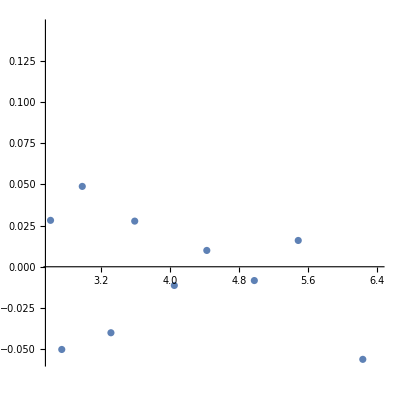

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%3,AspectRatio->1]
```